```mathematica
(*This notebook derives the logical chi matrix for Steane Code under iid rotation about Z
It tracks the diagonal and off diagonal contributions from original chi separately to get the impact of RC*)
```

```mathematica
ExpressionFromWeights[freqsWts_,n_,theta_]:=Total[Table[x[[1]]*(ⅈ Sin[theta])^(x[[2]])*(-ⅈ Sin[theta])^(x[[3]])*(Cos[theta]^(2*n - x[[2]] - x[[3]])),{x,freqsWts}],Infinity]
```

## L = I, L’ = I (new using wts)

No diagonal contribution in this case

```mathematica
n = 7;
totalFreqII = {1,7,7,49,7,28,21,28,21,112,84,84,63};
diagFreqII = {1,0,0,7,7,0,0,0,0,28,0,0,21};
offdiagFreqII = totalFreqII - diagFreqII;
wtlII = {0,0,4,4,1,1,1,3,5,3,5,3,5};
wtrII = {0,4,0,4,1,3,5,1,1,3,3,5,5};

freqsWtsOffII = MapThread[{#1,#2,#3}&,{offdiagFreqII,wtlII,wtrII}];
pIIoff = FullSimplify[ExpressionFromWeights[freqsWtsOffII,n,θ]];

freqsWtsdiagII = MapThread[{#1,#2,#3}&,{diagFreqII,wtlII,wtrII}];
pIIdiag = FullSimplify[ExpressionFromWeights[freqsWtsdiagII,n,θ]];

freqsWtsII = MapThread[{#1,#2,#3}&,{totalFreqII,wtlII,wtrII}];
pII = FullSimplify[ExpressionFromWeights[freqsWtsII,n,θ]];

(*Plot[pII/.{θ-> theta},{theta,0,Pi/2},PlotLabels->Automatic]*)
```

## L = I, L’ = Z

No diagonal contribution in this case

```mathematica
n = 7;
totalFreqIZ = {1,7,7,49,7,28,21,28,21,112,84,84,63};
wtlIZ = {0,0,4,4,1,1,1,3,5,3,5,3,5};
wtrIZ = {7,3,7,3,6,4,2,6,6,4,4,2,2};
freqsWtsIZ = MapThread[{#1,#2,#3}&,{totalFreqIZ,wtlIZ,wtrIZ}];
pIZoff = FullSimplify[ExpressionFromWeights[freqsWtsIZ,n,θ]];
pIZdiag = 0;
pIZ = pIZoff + pIZdiag;
```

## L = Z, L’ = I

No diagonal contribution in this case

```mathematica
n = 7;
totalFreqZI = {1,7,7,49,7,28,21,28,21,112,84,84,63};
wtlZI = {7,3,7,3,6,4,2,6,6,4,4,2,2};
wtrZI = {0,0,4,4,1,1,1,3,5,3,5,3,5};
freqsWtsZI = MapThread[{#1,#2,#3}&,{totalFreqZI,wtlZI,wtrZI}];
pZIoff = FullSimplify[ExpressionFromWeights[freqsWtsZI,n,θ]];
pZIdiag = 0;
pZI = pZIoff + pZIdiag;
```

## L = Z, L’ = Z

```mathematica
n = 7;
totalFreqZZ = {1,7,7,49,7,28,21,28,21,112,84,84,63};
diagFreqZZ = {1,0,0,7,7,0,0,0,0,28,0,0,21};
offdiagFreqZZ = totalFreqZZ - diagFreqZZ;
wtlZZ = {7,7,3,3,6,6,6,4,2,4,4,2,2};
wtrZZ = {7,3,7,3,6,4,2,6,6,4,2,4,2};

freqsWtsOffZZ = MapThread[{#1,#2,#3}&,{offdiagFreqZZ,wtlZZ,wtrZZ}];
pZZoff = FullSimplify[ExpressionFromWeights[freqsWtsOffZZ,n,θ]];

freqsWtsdiagZZ = MapThread[{#1,#2,#3}&,{diagFreqZZ,wtlZZ,wtrZZ}];
pZZdiag = FullSimplify[ExpressionFromWeights[freqsWtsdiagZZ,n,θ]];

freqsWtsZZ = MapThread[{#1,#2,#3}&,{totalFreqZZ,wtlZZ,wtrZZ}];
pZZ = FullSimplify[ExpressionFromWeights[freqsWtsZZ,n,θ]];
```

## Conditional channels and syndrome probabilities

### nonRC

```mathematica
chiS0II[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{totalFreqII[[1;;4]],wtlII[[1;;4]],wtrII[[1;;4]]}],n,θ];
chiS0IZ[θ_] :=ExpressionFromWeights[MapThread[{#1,#2,#3}&,{totalFreqIZ[[1;;4]],wtlIZ[[1;;4]],wtrIZ[[1;;4]]}],n,θ];
chiS0ZI[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{totalFreqZI[[1;;4]],wtlZI[[1;;4]],wtrZI[[1;;4]]}],n,θ];
chiS0ZZ[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{totalFreqZZ[[1;;4]],wtlZZ[[1;;4]],wtrZZ[[1;;4]]}],n,θ];
PrS0[θ_] := chiS0II[θ] + chiS0IZ[θ] + chiS0ZI[θ] + chiS0ZZ[θ];

(*Any syndrome i apart from 0; 1≤i≤ 7*)
chiSiII[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{totalFreqII[[5;;13]]/7,wtlII[[5;;13]],wtrII[[5;;13]]}],n,θ];
chiSiIZ[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{totalFreqIZ[[5;;13]]/7,wtlIZ[[5;;13]],wtrIZ[[5;;13]]}],n,θ];
chiSiZI[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{totalFreqZI[[5;;13]]/7,wtlZI[[5;;13]],wtrZI[[5;;13]]}],n,θ];
chiSiZZ[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{totalFreqZZ[[5;;13]]/7,wtlZZ[[5;;13]],wtrZZ[[5;;13]]}],n,θ];
PrSi[θ_] := chiSiII[θ]  + chiSiIZ[θ] + chiSiZI[θ] + chiSiZZ[θ];
```

```mathematica
Simplify[7*PrSi[θ] + PrS0[θ]] (* Checking total syndrome probability*)
```

1

### RC

```mathematica
chiRCS0II[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{diagFreqII[[1;;4]],wtlII[[1;;4]],wtrII[[1;;4]]}],n,θ];
chiRCS0ZZ[θ_] :=ExpressionFromWeights[MapThread[{#1,#2,#3}&,{diagFreqZZ[[1;;4]],wtlZZ[[1;;4]],wtrZZ[[1;;4]]}],n,θ];
PrRCS0[θ_] := chiRCS0II[θ] +  chiRCS0ZZ[θ];
(*Any syndrome i apart from 0; 1≤i≤ 7*)
chiRCSiII[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{diagFreqII[[5;;13]]/7,wtlII[[5;;13]],wtrII[[5;;13]]}],n,θ];
chiRCSiZZ[θ_] := ExpressionFromWeights[MapThread[{#1,#2,#3}&,{diagFreqZZ[[5;;13]]/7,wtlZZ[[5;;13]],wtrZZ[[5;;13]]}],n,θ];
PrRCSi[θ_] :=chiRCSiII[θ] + chiRCSiZZ[θ];
```

```mathematica
Simplify[7*PrRCSi[θ] + PrRCS0[θ]] (* Checking total syndrome probability*)
```

1

## Logical Chi matrix full without RC

```mathematica
LogchiWithoutRC={{pIIoff+pIIdiag,0,0,pIZdiag+pIZoff},{0,0,0,0},{0,0,0,0},{pZIdiag+pZIoff,0,0,pZZdiag+pZZoff}}
```

{{1/512 (256+231 Cos[2 θ]+49 Cos[6 θ]-21 Cos[10 θ]-3 Cos[14 θ])-21/64 Sin[2 θ] Sin[4 θ]^3,0,0,-1/8 ⅈ (2+9 Cos[4 θ]+3 Cos[8 θ]) Sin[2 θ]^3},{0,0,0,0},{0,0,0,0},{1/8 ⅈ (2+9 Cos[4 θ]+3 Cos[8 θ]) Sin[2 θ]^3,0,0,1/512 (256-231 Cos[2 θ]-49 Cos[6 θ]+21 Cos[10 θ]+3 Cos[14 θ])+21/64 Sin[2 θ] Sin[4 θ]^3}}

## Logical Chi matrix full with RC (only diagonal contributions remain)

```mathematica
LogchiWithRC = {{pIIdiag,0,0,pIZdiag},{0,0,0,0},{0,0,0,0},{pZIdiag,0,0,pZZdiag}}
```

{{1/512 (256+231 Cos[2 θ]+49 Cos[6 θ]-21 Cos[10 θ]-3 Cos[14 θ]),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1/512 (256-231 Cos[2 θ]-49 Cos[6 θ]+21 Cos[10 θ]+3 Cos[14 θ])}}

## Checking logical chi matrix validity

```mathematica
Plot[Eigenvalues[LogchiWithRC]/.{θ-> theta},{theta,0,Pi*2},PlotLabels->Automatic]
```

-Graphics-

```mathematica
Simplify[Total[Eigenvalues[LogchiWithRC],Infinity]]
```

1

```mathematica
Plot[Eigenvalues[LogchiWithoutRC]/.{θ-> theta},{theta,0,Pi*2},PlotLabels->Automatic]
```

-Graphics-

```mathematica
Simplify[Total[Eigenvalues[LogchiWithoutRC],Infinity]]
```

1

```mathematica
eigs =Table[ Eigenvalues[N[chinonRCLevelL[4,θ]]],{θ,0.1,0.8,0.07}]
```

{Eigenvalues[chinonRCLevelL[4.,0.1]],Eigenvalues[chinonRCLevelL[4.,0.17]],Eigenvalues[chinonRCLevelL[4.,0.24]],Eigenvalues[chinonRCLevelL[4.,0.31]],Eigenvalues[chinonRCLevelL[4.,0.38]],Eigenvalues[chinonRCLevelL[4.,0.45]],Eigenvalues[chinonRCLevelL[4.,0.52]],Eigenvalues[chinonRCLevelL[4.,0.59]],Eigenvalues[chinonRCLevelL[4.,0.66]],Eigenvalues[chinonRCLevelL[4.,0.73]],Eigenvalues[chinonRCLevelL[4.,0.8]]}

## Setting up recursion for withRC case

```mathematica
Expand[TrigExpand[LogchiWithRC[[1,1]]]/.{Sin[θ]-> Sqrt[1-(Cos[θ])^2]}]
```

21 Cos[θ]^4-98 Cos[θ]^6+210 Cos[θ]^8-252 Cos[θ]^10+168 Cos[θ]^12-48 Cos[θ]^14

```mathematica
Expand[TrigExpand[LogchiWithRC[[4,4]]]/.{Cos[θ]-> Sqrt[1-(Sin[θ])^2]}]
```

21 Sin[θ]^4-98 Sin[θ]^6+210 Sin[θ]^8-252 Sin[θ]^10+168 Sin[θ]^12-48 Sin[θ]^14

```mathematica
fRC[x_]:= 21 x^2 -98 x^3+210 x^4-252 x^5+168 x^6-48 x^7
```

```mathematica
chiRClevelL [l_,θ_]:= DiagonalMatrix[{Nest[fRC,Cos[θ]^2,l],0,0,Nest[fRC,Sin[θ]^2,l]}]
```

## Setting up recursion for nonRC case

```mathematica
Expand[TrigExpand[LogchiWithoutRC[[1,1]]]/.{Sin[θ]-> Sqrt[1-(Cos[θ])^2]}]
```

63 Cos[θ]^4-434 Cos[θ]^6+1260 Cos[θ]^8-1848 Cos[θ]^10+1344 Cos[θ]^12-384 Cos[θ]^14

```mathematica
Expand[TrigExpand[LogchiWithoutRC[[4,4]]]/.{Cos[θ]-> Sqrt[1-(Sin[θ])^2]}]
```

63 Sin[θ]^4-434 Sin[θ]^6+1260 Sin[θ]^8-1848 Sin[θ]^10+1344 Sin[θ]^12-384 Sin[θ]^14

```mathematica
fnonRCdiag[x_]:= 63 x^2 -434 x^3+1260 x^4-1848 x^5+1344 x^6-384 x^7
fnonRCoffdiagsupp[x_]:= 1/64 ⅈ (21 x - 14 (3 x - 4x^3) + 3(7 (1-x^2)^3 x-35 (1-x^2)^2 x^3+21 (1-x^2) x^5-x^7))
fnonRCoffdiag[y_]:= fnonRCoffdiagsupp[(-2/ⅈ) y]
```

```mathematica
chinonRC11levelL [l_,θ_]:= Nest[fnonRCdiag,Cos[θ]^2,l]
chinonRC44levelL[l_,θ_]:= Nest[fnonRCdiag,Sin[θ]^2,l]
chinonRC14levelL[l_,θ_]:=Nest[fnonRCoffdiag,-ⅈ Sin[2*θ]/2,l]
chinonRC41levelL[l_,θ_]:=Nest[fnonRCoffdiag,ⅈ Sin[2*θ]/2,l]
```

```mathematica
chinonRCLevelL[l_,θ_]:= Simplify[{{chinonRC11levelL[l,θ],0,0,chinonRC14levelL[l,θ]},{0,0,0,0},{0,0,0,0},{chinonRC41levelL[l,θ],0,0,chinonRC44levelL[l,θ]}}]
```

## Plot Settings

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
labelsize=2;
ticksize=18;
legendsize=2;
ell[l_]:=MaTeX[StringJoin["\\ell = ",ToString[l]],Magnification->legendsize];
labels=Table[ell[i],{i,1,5}];
(*Formatted log plot*)
FLogPlot[func__]:=LogPlot[func,RotateLabel->False,Frame->{True,True,True,True},FrameStyle->Thick,Axes->True,PlotStyle->Thickness[0.007],FrameTicksStyle->Directive["Label",ticksize],ImageSize->Large,PlotLegends-> labels, GridLinesStyle->Directive[Gray,Thickness[0.005],Dashed]]
```

#### Level 1 plot

```mathematica
MaTeX["r(\\overline{\\mathcal{E}}_{\\ell})",Magnification->labelsize]
```

```mathematica
pLevel1= FLogPlot[{(1-chiRClevelL[1,θ][[1,1]]),(1-chinonRC11levelL[1,θ])},{θ,0,Pi/5},FrameLabel->{MaTeX["\\theta",Magnification->labelsize],""},GridLines->{{thresh},{}},Epilog->{Text[Style[StringJoin["θ_c=", ToString[thresh]],FontSize->ticksize],{thresh + 0.0045,Log[0.001]}]},PlotLegends-> {MaTeX["r(\\overline{\\mathcal{E}^{T}}_{1})",Magnification->labelsize],MaTeX["r(\\overline{\\mathcal{E^T}}_{1})",Magnification->labelsize]}]
```

-Graphics-

```mathematica
Export["/home/oem/Desktop/Research_PhD/rcnotes/updates/figs/21Jan/pLevel1_only.pdf",pLevel1]
```

/home/oem/Desktop/Research_PhD/rcnotes/updates/figs/21Jan/pLevel1_only.pdf

## Infidelity plots

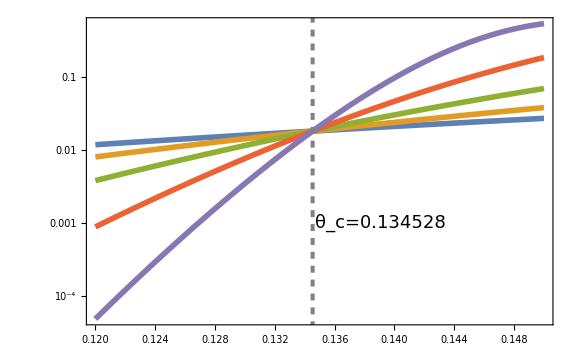

```mathematica
thresh=θ/.((FindInstance[chinonRC11levelL[1,θ] == chinonRC11levelL[2,θ]&&0<θ<π/4,θ,Reals]//N)[[1,1]]);
pinfnonRC = FLogPlot[Evaluate[Table[(1-chinonRC11levelL[i,θ]),{i,1,5}]],{θ,0.12,0.15},FrameLabel->{MaTeX["\\theta",Magnification->labelsize],MaTeX["r(\\overline{\\mathcal{E}}_{\\ell})",Magnification->labelsize]},GridLines->{{thresh},{}},Epilog->{Text[Style[StringJoin["θ_c=", ToString[thresh]],FontSize->ticksize],{thresh + 0.0045,Log[0.001]}]}]
```

```mathematica
Export["/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/infid_nonRC.pdf",pinfnonRC]
```

/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/infid_nonRC.pdf

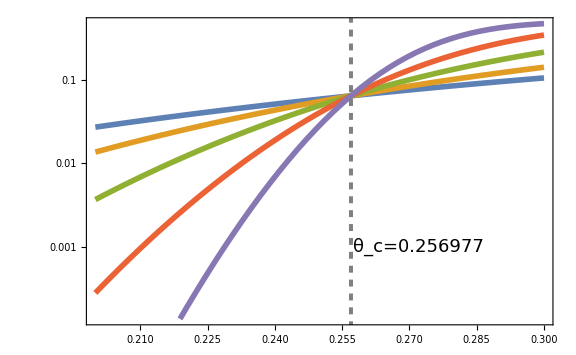

```mathematica
thresh=θ/.((FindInstance[chiRClevelL[1,θ] == chiRClevelL[2,θ]&&0.24<θ<0.28,θ,Reals]//N)[[1,1]]);
pinfRC = FLogPlot[Evaluate[Table[(1-chiRClevelL[i,θ][[1,1]]),{i,1,5}]],{θ,0.2,0.3},FrameLabel->{MaTeX["\\theta",Magnification->labelsize],MaTeX["r(\\overline{\\mathcal{E}^{T}}_{\\ell})",Magnification->labelsize]},GridLines->{{thresh},{}},Epilog->{Text[Style[StringJoin["θ_c=", ToString[thresh]],FontSize->ticksize],{thresh + 0.015,Log[0.001]}]}]
```

```mathematica
Export["/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/infid_RC.pdf",pinfRC]
```

/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/infid_RC.pdf

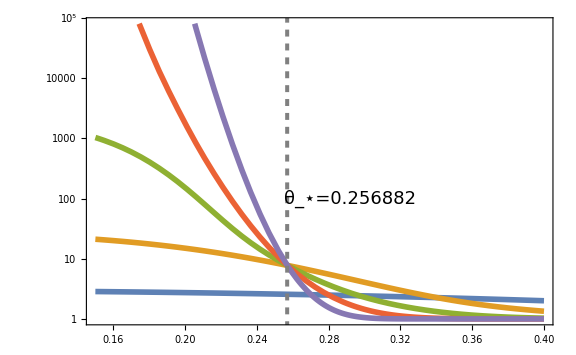

```mathematica
thresh=θ/.((FindInstance[(1-chinonRC11levelL[2,θ])/(1-chiRClevelL[2,θ][[1,1]]) == (1-chinonRC11levelL[3,θ])/(1-chiRClevelL[3,θ][[1,1]])&&0.24<θ<0.27,θ,Reals]//N)[[1,1]]);
pratioinf = FLogPlot[Evaluate[Table[(1-chinonRC11levelL[i,θ])/(1-chiRClevelL[i,θ][[1,1]]),{i,1,5}]],{θ,0.15,0.4},FrameLabel->{MaTeX["\\theta",Magnification->labelsize],MaTeX["\\delta_{\\ell}",Magnification->labelsize]},GridLines->{{thresh},{}},Epilog->{Text[Style[StringJoin["θ_⋆=", ToString[thresh]],FontSize->ticksize],{thresh + 0.035,Log[100]}]}]
(*where \delta_\ell=\\dfrac{r_{\\mathrm{non-RC}}}{r_{\\mathrm{RC}}}*)
```

```mathematica
Export["/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/ratio_infid.pdf",pratioinf]
```

/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/ratio_infid.pdf

## Diamond norm calculation using the average recursed channel

```mathematica
dnormnonRCLevelL[l_,θ_]:=Sqrt[(chinonRC44levelL[l,θ])^2 + (-ⅈ chinonRC14levelL[l,θ])^2]
```

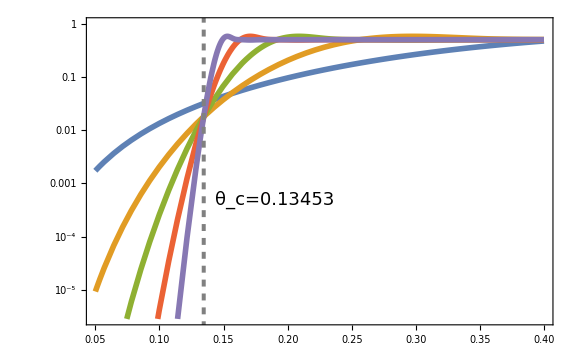

```mathematica
thresh=θ/.((FindInstance[dnormnonRCLevelL[2,θ]==dnormnonRCLevelL[3,θ]&&0.10<θ<0.15,θ,Reals]//N)[[1,1]]);
pdnormnonRC = FLogPlot[Evaluate[Table[dnormnonRCLevelL[l,θ],{l,1,5}]],{θ,0.05,0.4},FrameLabel->{MaTeX["\\theta",Magnification->labelsize],MaTeX["||\\overline{\\mathcal{E}}_{\\ell} - \\mathrm{id}||_{\\diamondsuit}",Magnification->labelsize*0.75]},GridLines->{{thresh},{}},Epilog->{Text[Style[StringJoin["θ_c=", ToString[thresh]],FontSize->ticksize],{thresh + 0.055,Log[0.0005]}]}]
```

```mathematica
Export["/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/dnorm_nonRC.pdf",pdnormnonRC]
```

/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/dnorm_nonRC.pdf

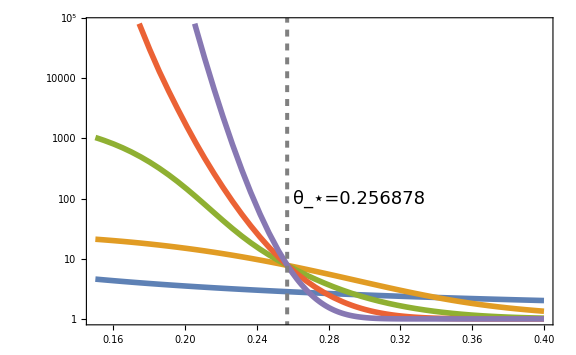

```mathematica
thresh=θ/.((FindInstance[(dnormnonRCLevelL[2,θ])/(chiRClevelL[2,θ][[4,4]])==(dnormnonRCLevelL[3,θ])/(chiRClevelL[3,θ][[4,4]])&&0.25<θ<0.27,θ,Reals]//N)[[1,1]]);
pratiodnorm = FLogPlot[Evaluate[Table[(dnormnonRCLevelL[l,θ])/(chiRClevelL[l,θ][[4,4]]),{l,1,5}]],{θ,0.15,0.4},FrameLabel->{MaTeX["\\theta",Magnification->labelsize],MaTeX["\\Delta_{\\ell}",Magnification->labelsize]},GridLines->{{thresh},{}},Epilog->{Text[Style[StringJoin["θ_⋆=", ToString[thresh]],FontSize->ticksize],{thresh + 0.04,Log[100]}]}]
(*\\Delta_{\\ell}=\\dfrac{\\Delta_{\\ell}^{\\mathrm{non-RC}}}{\\Delta_{\\ell}^{\\mathrm{RC}}}*)
(*where \\Delta_{\\ell}^{\\mathrm{non-RC}}=||\\overline{\\mathcal{E}}_{\\ell}^{\\mathrm{non-RC}} - \\mathrm{id}||_{\\diamondsuit}*)
```

```mathematica
Export["/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/ratio_dnorm.pdf",pratiodnorm]
```

/Users/pavi/Documents/rclearn/notes/updates/figs/21Jan/ratio_dnorm.pdf

## Approximation gone wrong (probably)

```mathematica
chimatRC[theta_]:=Simplify[LogchiWithRC/.{θ-> theta}]
chimatnonRC[theta_]:=Simplify[LogchiWithoutRC/.{θ-> theta}]
```

```mathematica
cutoff = 20;
sRC = (Series[chimatRC[θ],{θ,0,cutoff}])
sNonRC = Series[chimatnonRC[θ],{θ,0,cutoff}];
fidRCrec[θ_]:=(1+21 θ^4+112 θ^6-(1561 θ^8)/5+(26032 θ^10)/45-(525622 θ^12)/675+(1178816 θ^14)/1485-(6380272081 θ^16)/10135125+(7244004512 θ^18)/18243225-(225059807354 θ^20)/1107624375)/.{θ-> Sqrt[θ]}
fidnonRCrec[θ_]:=1-63 θ^4+476 θ^6-(8533 θ^8)/5+(18664 θ^10)/5-(3744266 θ^12)/675+(8872328 θ^14)/1485-(16484488931 θ^16)/3378375+(57017219536 θ^18)/18243225-(1785540861662 θ^20)/1107624375
fidRCLevelL[θ_,l_] := Nest[fidRCrec,θ,l]
fidnonRCLevelL[θ_,l_]:= Nest[fidnonRCrec,θ,l]
Plot[fidRCLevelL[θ,2],{θ,0,0.1},PlotLabels->Automatic]
```

{{1-21 θ^4+112 θ^6-(1561 θ^8)/5+(26032 θ^10)/45-(525622 θ^12)/675+(1178816 θ^14)/1485-(6380272081 θ^16)/10135125+(7244004512 θ^18)/18243225-(225059807354 θ^20)/1107624375+O[θ]^21,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,21 θ^4-112 θ^6+(1561 θ^8)/5-(26032 θ^10)/45+(525622 θ^12)/675-(1178816 θ^14)/1485+(6380272081 θ^16)/10135125-(7244004512 θ^18)/18243225+(225059807354 θ^20)/1107624375+O[θ]^21}}

-Graphics-

```mathematica
(Pi/18000)//N
```

0.000174533

```mathematica
fidRCrec[0.1]
```

1.00221

```mathematica
fidRCLevelL[0.1,2]
```

-22.8932

# Performance impact analysis

```mathematica
(*Polar decomposition of a matrix: https://mathematica.stackexchange.com/questions/71450/polar-decomposition*)
PD[m_]:={#.#3†,#3.#2.#3†}&@@SingularValueDecomposition[m];
```

```mathematica
p=0.05;
```

```mathematica
lkraus = 0.5*{{Sqrt[1-p],0},{0,Sqrt[1-p]}} + RandomReal[{-0.001,0.001},{2,2}];
```

```mathematica
{U,P}=PD[lkraus];
```

```mathematica
U.P-lkraus
```

{{5.55112×10^-17,-7.58942×10^-19},{3.57787×10^-18,1.66533×10^-16}}

```mathematica
Table[Tr[PauliMatrix[i].lkraus],{i,0,3}]
```

{0.974698,-0.000457762,0.+0.00103333 ⅈ,0.000979512}

```mathematica
Table[Tr[PauliMatrix[i].P],{i,0,3}]
```

{0.974699,-0.000456723,0.+0. ⅈ,0.000979997}